sWLC from Li et at, 2020
Re-viewing calculation
Lossless first, then lossy

```mathematica
(*sensitivity curve, using values from Fig.4-5 in Li et al, 2020
they choose to plot ((2 α^2 Subscript[S, h])/Subscript[γ, R])^(1/2)*)
Clear[α,χ,κ,γR];
α=1;
γR=2π 500 (*Hz*);
κ=10γR;
Sh[Ω_,χ_]:=((Ω^2+χ^2-κ^2)^2+Ω^2 γR^2)/(4 α^2 κ^2 γR)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
ASDScon[Ω_]:=((Ω^2+γR^2)/(4 α^2 γR) )^(1/2)(*given*)
(*signal and noise transfer functions:
Subscript[S, h]=(|R|^2+...+|Rc|^2)/(|T|^2), plot Subscript[S, h]^(1/2)=((|R|^2+...+|Rc|^2)^(1/2))/(|T|). Here, |T| and (|R|^2+...+|Rc|^2)^(1/2)*)
Tcon[Ω_]:=Abs[(-2I α γR^(1/2))/(Ω+I γR) ]
Rcon[Ω_]:=Abs[(Ω-I γR)/(Ω+I γR) ]
(*Labeled[LogLogPlot[{
(2/γR)^(1/2)ASDScon[ΩtoγR γR],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0.995κ],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=κ]},{ΩtoγR,0.15,35},ImageSize->400,PlotRange->{0.01,100},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"angular freq, Ω/γ_R / [1/γ_R]Hz (log scale)","strain sensitivity (NSR), ((2SuperscriptBox[α, 2]SubscriptBox[S, h])/γ_R)^(1/2)\n/ [α/γ_R^(1/2)]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
(*y-axis looks all wrong because we have scaled to α*)
(*Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.995κ],
ASDh[2π f,χ=κ]},{f,10/(2π),10^5/(2π)},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2 π) / Hz (log scale)","strain sensitivity (NSR), (α^2S_h)^(1/2)\n/ [α]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
Print["[old plot commented out]"]
```

[old plot commented out]

```mathematica
(*want to plot Sh^(1/2) against f using real values, to compare to sensitivity target
(recreating Fig.5 in Li et al, 2020 also requires radiation pressure noise, not yet derived)
This requires using the correct Subscript[α, GW] scale*)
Clear[α,χ,κ,γR];
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
Larm=4 10^3(*m*);
Pcirc=3 10^6(*J/s*);
λ0=2 10^-6(*m*);
ω0=2π c/λ0;
(*value in Li et al doesn't make sense dimensionally, using Korobko et al 2019 instead
α=((2Pcirc ℏ ω0)/(c Larm))^(1/2);*)
α=((2Pcirc Larm ω0)/(ℏ c))^(1/2);
γR=2π 500 (*Hz*);
κ=10γR;
(*Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.986κ],
ASDh[2π f,χ=κ]},{f,10,10^4},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2 π) / Hz (log scale)","strain sensitivity (NSR), S_h^(1/2)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
Print["[old plot commented out]"]
```

[old plot commented out]

Lossy sensitivity, adding loss terms to each mode, assuming each noise is quantum with uncorrelated vacuum bath

```mathematica
(*semi-automated plotting*)
(*separating losses and making transmittivities inputs*)
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
τRoundTripArm=(2 Larm)/c;
γa[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
(*Assuming LIGO Voyager's Subscript[T, SRM] was used for γR
this is different to above for the threshold plots where I assumed the LIGO value of 56m was used for Subscript[L, SRC]*)
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];(*Subscript[γ, R]=-1/(2 τRoundTripSRC)Log[1-Tsrm]*)
γb[Tlb_]:=-1/(2 τRoundTripSRC)Log[1-Tlb]
γbtot[Tlb_]:=γR+γb[Tlb]
(*assuming that c mode is also in SRC, e.g. non-degenerate internal squeezing*)
γc[Tlc_,symSRM_:False]:=If[symSRM,γR+-1/(2 τRoundTripSRC)Log[1-Tlc],-1/(2 τRoundTripSRC)Log[1-Tlc]]
(*symSRM=True: i.e. γctot[Tlc_]:=γR+γc0[Tlc], symmetric SRM loss assumption*)
TsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[((-2α κ γR^(1/2))/(γa[Tla]-I Ω))/(γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω))]
RsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=((1-Rpd)(
Abs[γbtot[Tlb]-2γR-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]^2
+Abs[(-2(γR γa[Tla])^(1/2)κ)/(γa[Tla]-I Ω)]^2
+Abs[-2(γR γb[Tlb])^(1/2)]^2
+Abs[(2(γR γc[Tlc,symSRM])^(1/2)χ)/(γc[Tlc,symSRM]-I Ω)]^2)/Abs[γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]^2+Rpd)^(1/2)
ASDShsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1/((γc[Tlc,symSRM]^2+Ω^2)4 α^2 κ^2 γR)(
((γbtot[Tlb]-2γR)(γa[Tla] γc[Tlc,symSRM]-Ω^2)-(γa[Tla]+γc[Tlc,symSRM])Ω^2+κ^2 γc[Tlc,symSRM]-χ^2 γa[Tla])^2
+Ω^2(χ^2-κ^2-(γbtot[Tlb]-2γR)(γa[Tla]+γc[Tlc,symSRM])-γa [Tla]γc[Tlc,symSRM]+Ω^2)^2
+4γR γa[Tla] κ^2(γc[Tlc,symSRM]^2+Ω^2)
+4γR γb[Tlb](γa[Tla]^2+Ω^2)(γc[Tlc,symSRM]^2+Ω^2)
+4γR γc[Tlc,symSRM] χ^2(γa[Tla]^2+Ω^2)
+Rpd/(1-Rpd)((γbtot[Tlb](γa[Tla] γc[Tlc,symSRM]-Ω^2)-(γa[Tla]+γc[Tlc,symSRM])Ω^2+κ^2 γc[Tlc,symSRM]-χ^2 γa[Tla])^2
+Ω^2(χ^2-κ^2-γbtot[Tlb](γa[Tla]+γc[Tlc,symSRM])-γa [Tla]γc[Tlc,symSRM]+Ω^2)^2)))^(1/2)

(*plotting*)
(*vals={χ, Tla, Tlb, Tlc, Rpd}*)
labeller[vals_,symSRM_:False]:=(
paddedStrings=StringPadRight[{ToString[N[vals[[1]]/κ]],ToString[vals[[2]]],ToString[vals[[3]]],ToString[vals[[4]]],ToString[vals[[5]]]},4];
If[symSRM,
Style[StringForm["χ/κ=``; T_(l, a)=``, T_(l, b)=``, γ_(c, tot)=γ_R+γ_(c, loss port)(T_(l, c)=``), R_PD=``",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],FontFamily->"Monospace"],
Style[StringForm["χ/κ=``; T_(l, a)=``, T_(l, b)=``, T_(l, c)=``, R_PD=``",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],FontFamily->"Monospace"]]
(*search for mono-spaced fonts in: $FontFamilies*)
)
plotsWLC[valsList_,plotLabel_:"optical stable WLC",plotStyle_:{},symSRM_:False]:=(
p1=LogLinearPlot[Evaluate[Join[
{20Log10[Rcon[2π f]]},
Table[20Log10[RsWLC@@Join[{2π f},valsList[[i]],{symSRM}]],{i,1,Length[valsList]}]]]
,{f,10,10^4},ImageSize->350,PlotLegends->LineLegend[Join[{"lossless conventional"},Table[labeller[valsList[[i]],symSRM],{i,1,Length[valsList]}]],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{90,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->If[plotStyle=={},Join[{Directive[Gray,DotDashed]},Table[,{n,1,Length[valsList]}]],Join[{Directive[Gray,DotDashed]},plotStyle]],Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,plotLabel}}];
p2=LogLogPlot[Evaluate[Join[
{Tcon[2π f]},
Table[TsWLC@@Join[{2π f},valsList[[i]],{symSRM}],{i,1,Length[valsList]}]]],{f,10,10^4},ImageSize->350,PlotLegends->LineLegend[Join[{"lossless conventional"},Table[labeller[valsList[[i]],symSRM],{i,1,Length[valsList]}]],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],ImagePadding->{{90,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->If[plotStyle=={},Join[{Directive[Gray,DotDashed]},Table[,{n,1,Length[valsList]}]],Join[{Directive[Gray,DotDashed]},plotStyle]],Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[Evaluate[Join[
{ASDScon[2π f]},
Table[ASDShsWLC@@Join[{2π f},valsList[[i]],{symSRM}],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,10,10^4},ImageSize->350,ImagePadding->{{90,10},{50,1}},PlotLegends->LineLegend[Join[{"lossless conventional"},Table[labeller[valsList[[i]],symSRM],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->If[plotStyle=={},Join[{Directive[Gray,DotDashed]},Table[,{n,1,Length[valsList]}],{Directive[Red,DotDashed]}],Join[{Directive[Gray,DotDashed]},plotStyle,{Directive[Red,DotDashed]}]],PlotRange->{{10,10^4},All},Filling->{Length[valsList]+2->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0])
(*PlotStyle->{Directive[Gray,DotDashed],Gray,,Dashed,,Dashed,Directive[DotDashed,Red]}*)
```

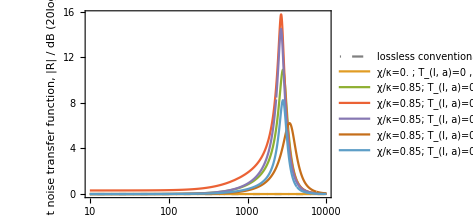
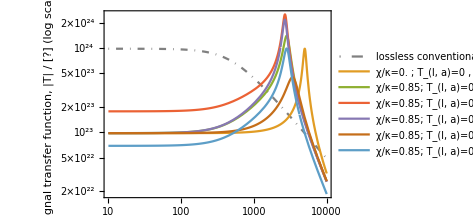
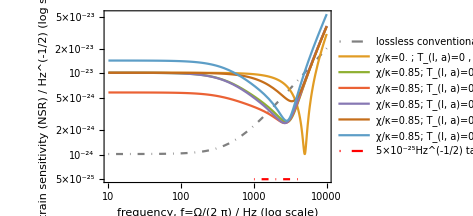

```mathematica
χRatio0=0.85;
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
valsList0={
{0κ,0,0,0,0},
{χRatio0 κ,0,0,0,0},
{χRatio0 κ,0.1,0,0,0},
{χRatio0 κ,0,0.1,0,0},
{χRatio0 κ,0,0,0.1,0},
{χRatio0 κ,0,0,0,0.5}};
plotsWLC[valsList0,"optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects",
{},True](*with sym SRM*)
(*to-do: figure what is going on with shot noise, why doesn't it appear unless γc≠0?*)
```

```mathematica
(*copying from degIntSqz.nb*)
{f0, f1} = {1 10^3,4 10^3};(*Hz*)
ASDShCrit = 5 10^-25;(*Hz^(-1/2)*)
ShCrit=ASDShCrit^2;(*Hz^-1*)
μtricK[fnSh_,K_]:=1/(f1-f0)NIntegrate[(1/fnSh[2π f]-1/ShCrit)/(1/ShCrit)K[f],{f,f0,f1}]
printμtricK[fnSh_,K_]:=Print[StringForm["For S_h(Ω) given by: ``\nK=``\n--> μtricK=`` (unitless)",fnSh,K,NumberForm[μtricK[fnSh,K]]]]
μtric1[fnSh_]:=μtricK[fnSh,1&]
(*use k1=1/9 in order for Z=10 Subscript[Z, 0] to correspond to K=1/ⅇ*)
KExpk1[fnSh_,f_,k1_:1/9]:=(
Z=(1/fnSh[2π f]-1/ShCrit)/(1/ShCrit);
If[Z>0,Exp[-k1 Z],1])
μtricExpk1[fnSh_,k1_:1/9]:=μtricK[fnSh,KExpk1[fnSh,#,k1]&]
(*//end of copied code*)

(*

(*symSRM=False throughout,
to-do: try with symSRM=True*)
reduSh1[Ω_?NumericQ,r_?NumericQ]:=ASDShsWLC[Ω,r κ,0,0,0,0]^2
opti1Fn[r_?NumericQ]:=μtric1[reduSh1[#,r]&]
opti1Vals=FindMaximum[{opti1Fn[r],0<r<1},r]
printμtricK[reduSh1[#,r/.opti1Vals[[2]][[1]]]&,1&]

k11=1/9;
optiExpk1Fn[r_?NumericQ]:=μtricExpk1[reduSh1[#,r]&,k11]
optiExpk1Vals1=FindMaximum[{optiExpk1Fn[r],0<r<1},r]
reduSh1Opti=reduSh1[#,r/.optiExpk1Vals1[[2]][[1]]]&
printμtricK[reduSh1Opti,KExpk1[reduSh1Opti,#,k11]&]

k12=100;
optiExpk1Fn[r_?NumericQ]:=μtricExpk1[reduSh1[#,r]&,k12]
optiExpk1Vals2=FindMaximum[{optiExpk1Fn[r],0<r<1},r,MaxIterations->5]
reduSh1Opti=reduSh1[#,r/.optiExpk1Vals2[[2]][[1]]]&
printμtricK[reduSh1Opti,KExpk1[reduSh1Opti,#,k12]&]
-Graphics-;
(*optimisation finds values off threshold*)
plotsWLC[{
{0κ,0,0,0,0},
{(r/.opti1Vals[[2]][[1]]) κ,0,0,0,0},
{(r/.opti1Vals[[2]][[1]]) κ,0.1,0,0,0},
{(r/.optiExpk1Vals1[[2]][[1]]) κ,0,0,0,0},
{(r/.optiExpk1Vals1[[2]][[1]]) κ,0.1,0,0,0},
{(r/.optiExpk1Vals2[[2]][[1]]) κ,0,0,0,0},
{(r/.optiExpk1Vals2[[2]][[1]]) κ,0.1,0,0,0}},"optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects",{,,,Dashed,Dashed,DotDashed,DotDashed}]
Print[StringForm["μ1 is solid; μK1: k1=`` is dashed, k1=`` is dot-dashed",k11,k12]]

*)
```

lossless: {{Ω→1/2 ⅈ (-γR0+√(γR0^2-4 κ0^2+4 χ0^2))},{Ω→-1/2 ⅈ (γR0+√(γR0^2-4 κ0^2+4 χ0^2))}}

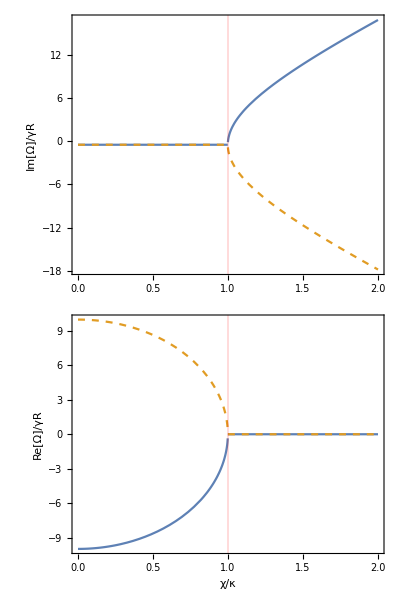

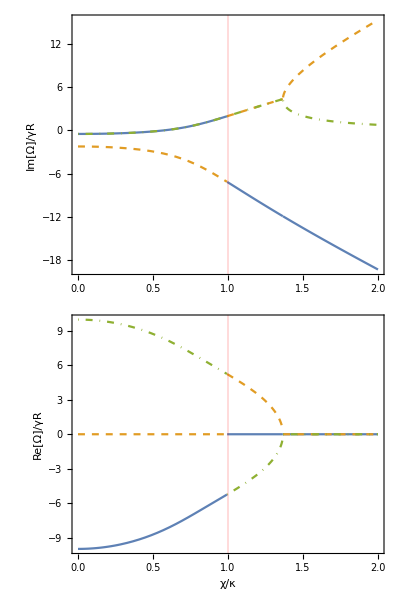

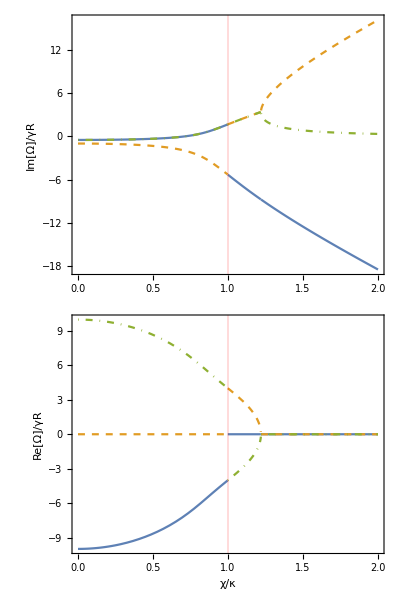

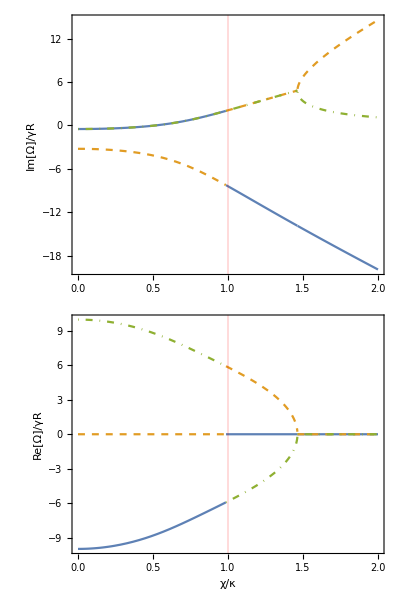

```mathematica
(*Checking stability*)
Clear[χ]
denominator=γbtot0-I Ω+κ0^2/(γa0-I Ω)-χ0^2/(γc0-I Ω);(*additional poles at γa,γc*)
Print["lossless: ",Solve[(denominator/.{γa0->0,γc0->0,γbtot0->γR0})==0,Ω]]
(*stabilitySol=Simplify[Solve[denominator==0,Ω],Assumptions->{κ0>0,χ0>0,γa0>0,γbtot0>0,γc0>0}];*)
denom[Tla_,Tlb_,Tlc_,symSRM_:False]:=γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω);

stabilitysWLC[Tla_,Tlb_,Tlc_,symSRM_:False]:=(
sol=NSolve[denom[Tla,Tlb,Tlc,symSRM]==0,Ω];
p1=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio κ})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,StringForm["poles of transfer function\nunstable when Im[Ω]≥0\nT_(l, a)=``, T_(l, b)=``, T_(l, c)=``, sym. SRM loss?=``",Tla,Tlb,Tlc,symSRM]}},GridLines->{{{1,Red}},None}];
p2=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio κ})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/κ",}},GridLines->{{{1,Red}},None}];
Column[{p1,p2}])
(*Manipulate[stabilitysWLC[Tla,Tlb,Tlc],{Tla,0,1},{Tlb,0,1},{Tlc,0,1}]*)
(*If the Manipulate is not working, then run the cell again*)
(*Tla_,Tlb_,Tlc_*)
stabilitysWLC[0,0,0]
stabilitysWLC[0,0,0.1]
stabilitysWLC[0,0,0,True]
stabilitysWLC[0,0,0.1,True]
Clear[Tla,Tlb,Tlc]
(*realistically, γc is at least γR, so the lossless plot is not useful*)
```

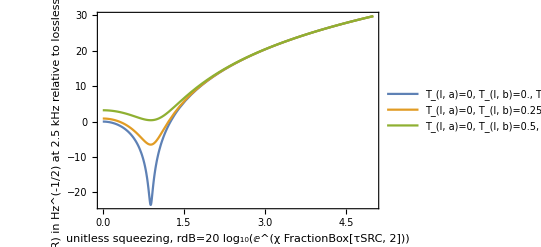

rdB→0.885581

To a tolerance of 1.×10^-5, the optimum χ is on threshold: False

χOpti=27207., κ=31415.9, χOpti/κ=0.866025

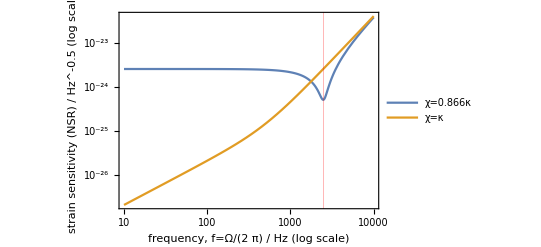

```mathematica
(*sensitivity at 2.5 kHz versus squeezer parameter, like deg.int.sqz. plot,
symSRM=False throughout*)
fProbe=2.5 10^3(*Hz*);
sensRef =ASDShsWLC[2π fProbe,0,0,0,0,0];

TlaList={0};
TlbList=Range[0,0.5,0.25];
TlcList={0};

Plot[Evaluate[Table[20Log10[ASDShsWLC[2π fProbe,2/τRoundTripSRC Log[10^(rdB/20)],TlaList[[i]],TlbList[[j]],TlcList[[k]],0]/sensRef]
,{i,1,Length[TlaList]},{j,1,Length[TlbList]},{k,1,Length[TlcList]}]],{rdB,0,5},PlotLegends->LineLegend[Flatten[Table[StringForm["T_(l, a)=``, T_(l, b)=``, T_(l, c)=``",TlaList[[i]],TlbList[[j]],TlcList[[k]]],{i,1,Length[TlaList]},{j,1,Length[TlbList]},{k,1,Length[TlcList]}]],LabelStyle->Directive[10]],Frame->True,FrameLabel->{{StringForm["strain sensitivity (NSR) in Hz^(-1/2) at `` kHz\nrelative to lossless, no squeezing value / dB",fProbe/10^3],},{"unitless squeezing, rdB=20 log_10(ⅇ^(χ FractionBox[τSRC, 2]))","optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager"}}]

(*showing that minimum is indeed χ=kout*)
thresholdrdB = N[Minimize[{20Log10[ASDShsWLC[2π fProbe,2/τRoundTripSRC Log[10^(rdB/20)],0,0,0,0]/sensRef],rdB>0},{rdB}][[2]][[1]]]
thresholdχ=2/τRoundTripSRC Log[10^(rdB/20)]/.thresholdrdB;
tolerance=N[10^-5];
Print[StringForm["To a tolerance of ``, the optimum χ is on threshold: ``",ScientificForm[tolerance],Abs[(thresholdχ-κ)/κ]<tolerance]]
Print[StringForm["χOpti=``, κ=``, χOpti/κ=``",NumberForm[thresholdχ],NumberForm[N[κ]],NumberForm[thresholdχ/N[κ]]]]
(*Manipulate[LogLogPlot[ASDhPDLossy[2π f,χ=rat κ,lossRatio=0,Rpd=0],{f,10,10^4},PlotRange->{10^-27,10^-22},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2 π) / Hz (log scale)",StringForm["above process optimises for sensitivity at `` kHz\nnot for overall bandwidth\nχ/κ=``",fProbe/10^3,χ/κ]}},GridLines->{{{fProbe,Red}},None}],{{rat,thresholdχ/N[κ],"χ/κ"},0,2}]*)
LogLogPlot[{
ASDShsWLC[2π f,χ=thresholdχ ,0,0,0,0],
ASDShsWLC[2π f,χ=κ,0,0,0,0]},{f,10,10^4},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",StringForm["sWLC - lossless\nabove process optimises for sensitivity at `` kHz\nnot for overall bandwidth",fProbe/10^3]}},GridLines->{{{fProbe,Red}},None},PlotLegends->{StringForm["χ=``κ",NumberForm[thresholdχ/N[κ],4]],"χ=κ"}]
```

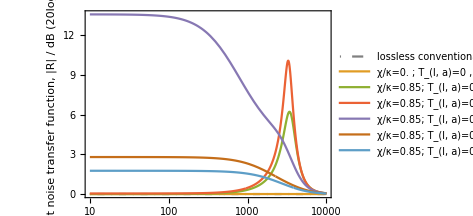
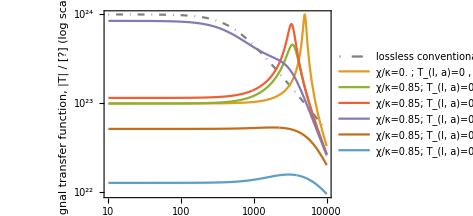
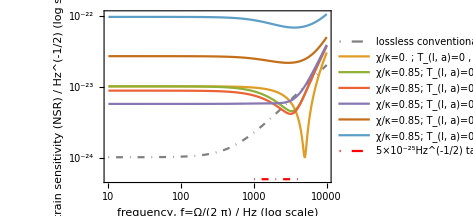

```mathematica
χRatio0=0.85;
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
valsList0={
{0κ,0,0,0,0},
{χRatio0 κ,0,0,0.1,0},
{χRatio0 κ,0.1,0,0.1,0},
{χRatio0 κ,0.5,0,0.1,0},
{χRatio0 κ,0.9,0,0.1,0},
{χRatio0 κ,0.999,0,0.1,0}};
plotsWLC[valsList0,"optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects",{},True]
```

```mathematica
(*splitting noise budget*)
RinsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[γbtot[Tlb]-2γR-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]/Abs[γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlasWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[(-2(γR γa[Tla])^(1/2)κ)/(γa[Tla]-I Ω)]/Abs[γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlbsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[-2(γR γb[Tlb])^(1/2)]/Abs[γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlcsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[(2(γR γc[Tlc,symSRM])^(1/2)χ)/(γc[Tlc,symSRM]-I Ω)]/Abs[γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlpdsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=Rpd^(1/2)
(*RIntExtSqz=sum of above four in quadrature*)
(*https://mathematica.stackexchange.com/questions/10833/how-do-i-convert-an-argument-list-to-a-sequence-of-arguments
@@ is infix Apply[f,{a,b,c,d}]*)
noiseBudgetsWLC[params_,symSRM_:False]:=
LogLinearPlot[{
20Log10[1],
20Log10[RinsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlasWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlbsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlcsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlpdsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RsWLC@@Join[{2π f},params,{symSRM}]]},{f,10,10^4},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_c, SRC idler intra-cav.","(R^(L))_PD, PD loss","total shot noise"},LabelStyle->Directive[10],LegendLabel->labeller[params,symSRM]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2  π) / Hz","optical sWLC\nparameters of LIGO Voyager"}}]
```

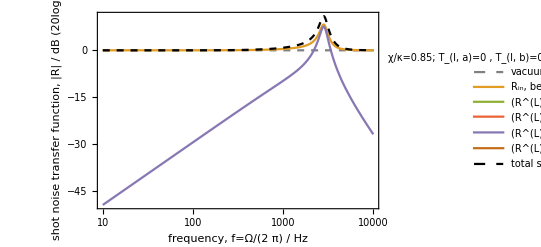

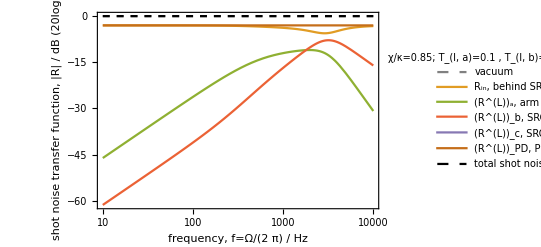

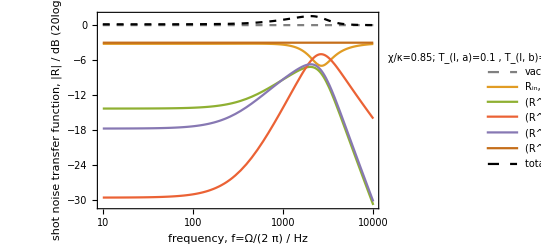

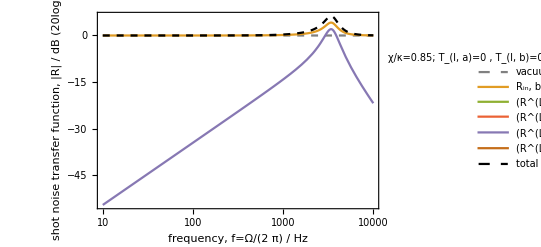

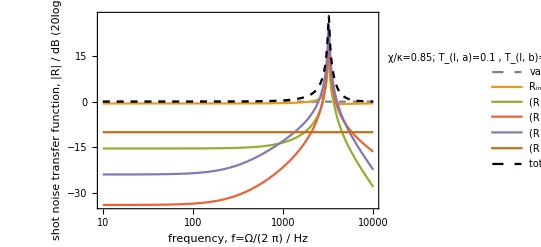

```mathematica
(*χ_,Tla_,Tlb_,Tlc_,Rpd_*)
χRatio0=0.85;
noiseBudgetsWLC[{χRatio0 κ,0,0,0,0},True]
noiseBudgetsWLC[{χRatio0 κ,0.1,0.2,0,0.5},False]
noiseBudgetsWLC[{χRatio0 κ,0.1,0.2,0,0.5},True]
noiseBudgetsWLC[{χRatio0 κ,0,0,0.1,0},True]
noiseBudgetsWLC[{χRatio0 κ,0.1,0.1,0.1,0.1},True]
```

```mathematica
(*like deg. int. sqz. and degenerate OPO:
comparing shot noise to nondegenerate OPO variance in limit of arm cavity loss -> 1,
does the three mirror system reduce to a two mirror system of the SRM and ITM?*)

(*in limit of Tla->1*)
SX2out=Rpd1+(1-Rpd1)(
(γc1(γbtot1-2γR1)-Ω1^2-χ1^2)^2
+Ω1^2(γbtot1-2γR1+γc1)^2
+4 γR1 γb1 (γc1^2+Ω1^2)
+4 γR1 γc1 χ1^2
)/((γc1 γbtot1-Ω1^2-χ1^2)^2
+Ω1^2(γbtot1+γc1)^2);
Assumps3={γc1>0,γR1>0,γbtot1>=γR1,Ω1>0,χ1>0};
FullSimplify[SX2out/.{γb1->γbtot1-γR1},Assumptions->Assumps3]
(*which agrees with NOPO (see calculation with asymmetric losses)!*)
```

1-(8 (-1+Rpd1) γc1 γR1 χ1^2)/((-γbtot1 γc1+χ1^2)^2+(γbtot1^2+γc1^2+2 χ1^2) Ω1^2+Ω1^4)

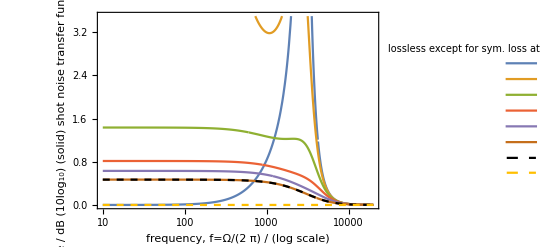

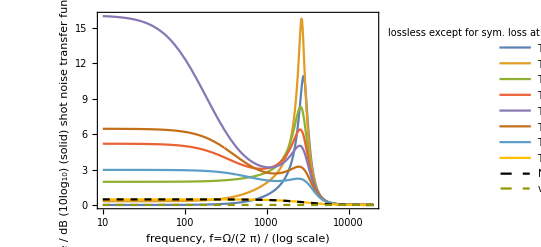

```mathematica
(*to match original NOPO calculation, need symmetric losses γc=γbot=γR+γb
have now shown that asymmetric losses also matches.
therefore, should have γctot=γR+γc where γc is now the added loss (i.e. making the SRM loss symmetric) -- we have shown in the NOPO case that we are free to split the loss like this as long as we only care about detecting b mode at the output*)
NOPOV22symSRM[Ω_,g_,Tlb_:0,Tlc_:0,Rpd_:0]:=(
(*looking at formal limit of Tla->1, noise in the â mode also shuts off
-- the equivalent of making Titm perfect, not a vacuum port
-- why isn't power still lost through Titm, term vanishes with â?*)
κaf=γR;(*uses Tse and Lse*)
κar=0;
κal=γb[Tlb];
κa=κaf+κar+κal;(*γbtot[Tloss]*)
(*assuming that the SRM loss is symmetric between b and c, else the variance is just 1*)
κc=γc[Tlc,True];(*γctot[Tlc]=γR+γc0[Tlc]*)
(*this formula is agnostic towards where the ĉ noise originates*)
1+(8 (1-Rpd) κaf κc Abs[g]^2)/((κa κc-Abs[g]^2)^2+Ω^2 (κa^2+κc^2+2 Abs[g]^2)+Ω^4)) 

(*plotting*)
χRatio0=0.85;
plotArmLossLimitSymSrm[armLossList_,plotRange_:Automatic]:=
LogLinearPlot[Evaluate[Join[
Table[
20Log10[RsWLC[2π f,χRatio0 κ,armLossList[[i]],0,0,0,True]](*symSRM=True to match NOPO*)
,{i,1,Length[armLossList]}],
{10Log10[NOPOV22symSRM[2π f,χRatio0 κ]],
10Log10[1]}]],
{f,10,2 10^4},PlotRange->plotRange,PlotLegends->LineLegend[Join[
Table[StringForm["T_(l, a)=``",N[armLossList[[i]]]]
,{i,1,Length[armLossList]}],
{"NOPO V_22","vacuum"}],LabelStyle->Directive[10],LegendLabel->StringForm["lossless except for sym. loss at SRM\nlast loss is T_(l, a)=1-``",ScientificForm[N[ϵ]]]],PlotStyle->Join[Table[{,},{i,1,Length[armLossList]}],{Directive[Black,Dashed],Dashed}],Frame->True,FrameLabel->{{ "(dashed) variance / dB (10log_10)\n(solid) shot noise transfer function\n|R| / dB (20log_10)",},{"frequency, f=Ω/(2  π) / (log scale)","sWLC reducing to nondegenerate OPO when T_(l, a)->1\nusing parameters of reduced two-mirror system (SRM and ITM)\nbut with T_ITM=0 as entire â mode vanishes\nassuming symmetric loss at SRM, i.e. γctot=γR+γc≠0"}}]
ϵ=10^-100;
armLossList=Join[Range[0,0.9,0.2],{1-ϵ}];
plotArmLossLimitSymSrm[armLossList]
plotArmLossLimitSymSrm[Join[{0,0.1,0.15,0.175,0.2,0.25,0.3},{1-ϵ}],All]
```